## PHAS2443: Practical Mathematics II 2017/2018 Homework 1 Hayk Khachatryan - 15013904

## Question 1

```mathematica
Clear[getOutLower]
getOutLower = ("a"|"e"|"i"|"o" |"u") -> Nothing;
```

```mathematica
{"g", "u", "e", "l", "y", "e", "i", "p", "h", "a", "a"} //.getOutLower
```

{g,l,y,p,h}

## Question 2

```mathematica
Clear[factorial]
factorial[0] := 1
factorial[q_Integer /; q > 0] := q factorial[q-1]
```

```mathematica
myTiming = Timing[factorial[50]][[1]];
mathematicaTiming = Timing[Factorial[50]][[1]];
howLong = mathematicaTiming / myTiming;
Print["My function takes ~", howLong, " as long as the built in Mathematica function to compute 50! (", myTiming, "s vs ", mathematicaTiming, "s)"]
```

My function takes ~0.0143369 as long as the built in Mathematica function to compute 50! (0.000279s vs 4.×10^-6s)

## Question 3

```mathematica
cycler[list_List, nests_Integer]:=

NestList[ (* apply the algorithm to a list, keeping a history *)

ListConvolve[  (* convolute over the list with our algorithm *)

{1,1,1},  (* kernel *)
#,                   (* pure function value received from NestList *)
2,                   (* align the convolution to an element and its two neighbors *)
#,                   (* default padding value (the list) to have cyclic permutations *)
Times,          (* multiply the kernel and list elements *)

If[                   (* Returns the sum of our list element + 2 neighbors, or the Mod[sum,3] *)
(#1+#2+#3) <3,    (* if the sum of the list element and its two neighbors < 3 *)
#1+#2+#3,                 (* return the sum *)
Mod[#1+#2+#3,3]   (* else return the mod of the sum with 3 *)   
] &

] &,

list, (* passed to ListConvolve as the list *)
nests   (* how many times to nest *)
]
```

```mathematica
S = {0,0,0,0,0,1,0,0,0,0,0};
ArrayPlot[cycler[S, 150]]
```

-Graphics-

It seems to begin repeating itself towards the end

```mathematica
distinctions[u_Integer]:= 
Length[                
Union[                 (* remove repeat configurations *)
cycler[S,u] (* run cycler with S and u nests *)
]]
```

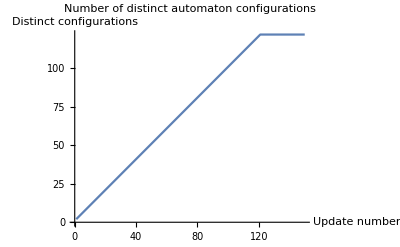

```mathematica
ListPlot[Table[{x, distinctions[x]}, {x, 1, 150}], Joined -> True, AxesLabel->{"Update number", "Distinct configurations"}, PlotLabel-> "Number of distinct automaton configurations"]
```